```mathematica
[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive
```

# Формулы

```mathematica
"Символы"paclet:tutorial/LettersAndLetterLikeForms
```

( = esc)

a → α
b → β
γ → γ
…
f → ϕ    j → φ
e → ϵ  ce → ε
w → ω  o → ω     om → ο

deg  → °

```mathematica
α β ϕ φ
```

α β ϕ φ

```mathematica
"Набор формул"paclet:tutorial/KeyboardShortcutListing#1484044289
```

Ctrl+6 → □^□
Ctrl+2 → √□
…+Ctrl+5 → □^(1/□)
Ctrl+/→ □/□
Ctrl+Space → end subexpression
Alt+/→ (*comment*)

Alt+ ),],}→ (),[],{}
Ctrl+,→  | □ | □ | □
Ctrl+Enter → □
□
□
…→(□ | □ | □
□ | □ | □
□ | □ | □)

# Выражения

```mathematica
"Everything is an Expression"paclet:tutorial/EverythingIsAnExpression
```

Head[a_1, a_2, a_3,…]

```mathematica
FullForm[a+b]
```

Plus[a,b]

```mathematica
F[x,y]
```

F[x,y]

```mathematica
"Expressions"paclet:tutorial/ExpressionsOverview
```

Head[]
FullForm[]
TreeForm[]

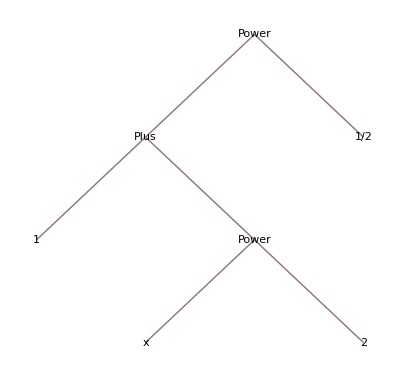

```mathematica
TreeForm[√(1+x^2)]
```

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

Для вызова справки выделить имя и нажать F1
Part[] - ⟦⟧      (* ⟦ ← [[ , ⟧ ← ]] *)
Range[]
Table[]
Subdivide[]

# Правила преобразования

```mathematica
2+2
```

4

```mathematica
2+x
```

2+x

Задание правил

```mathematica
x=4;
```

```mathematica
?x
```

Global`x

x=4

```mathematica
2+x
```

6

Удаление всех правил, ассоциированных с символом

```mathematica
Clear[x]
```

```mathematica
?x
```

Global`x

Set[]  (=)
SetDelayed[]  (:=)

Простое задание правила через = не подходит для определения функций, поскольку вычисляет правую часть до создания правила

```mathematica
x=2;
F[x_]=x^2;
F[3]
```

4

правило с отложенным вычислением

```mathematica
F[x_]:=x^2;
F[3]
```

9

```mathematica
F[0]:=5;
F[x_]:=x^2;
F[x_,_]:=x^3;
```

```mathematica
?F
```

Global`F

F[0]:=5
 
F[x_]:=x^2
 
F[x_,_]:=x^3

```mathematica
F[0]
```

5

```mathematica
F[3]
```

9

```mathematica
F["kjhsdgfkjh"]
```

kjhsdgfkjh^2

```mathematica
F[0]:=0;
F[1]:=1;
F[n_]:=F[n-1]+F[n-2];  (*определение с использованием рекурсии*)
{F[0],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8],F[9]}
```

{0,1,1,2,3,5,8,13,21,34}

```mathematica
"Patterns"paclet:tutorial/PatternsOverview
```

"Specifying Types"paclet:tutorial/SpecifyingTypesOfExpressionInPatterns (F[x_type]:=…)
Optional (F[x_:x0]:=…)
PatternTest (F[x_?test]:=…)
Optional with PattenTest (F[x:(_?test):x0]:=…)
Condition (F[x_/;test]:=…)

Sequence of variables (F[x__]:=…)
Parameterized function(F[α_][x_]:=…)
…

Применение функции к списку аргументов = замена заголовка List именем функции:

```mathematica
Apply[F,{s,5}]
```

s^3

краткая запись

```mathematica
F@@{s,5}
```

s^3

```mathematica
ArcTan@@(a+b)
```

ArcTan[a,b]

```mathematica
Clear[F];
```

Три эквивалентных способа записи применения функции к одному аргументу

```mathematica
F@(a)
F[a]
(a)//F
```

F[a]

F[a]

F[a]

```mathematica
"(порядок применения операторов при преобразовании к полной форме)"paclet:tutorial/OperatorInputForms
```

Безымянные (анонимные) функции

```mathematica
Function[{x,y,z},z+y^2]
```

Function[{x,y,z},z+y^2]

```mathematica
Function[{x,y,z},z+y^2][4,5,6]
Function[{x,y,z},z+y^2]@@{4,5,6}
```

31

31

краткая запись с использованием безымянных аргументов

```mathematica
(#^2)&
(#1^2+#2)&
```

#1^2&

#1^2+#2&

```mathematica
(#^2)&@5
```

25

```mathematica
(#1^2+#2)&@@{5,3}
```

28

```mathematica
(*использование анонимной функции в качестве аргумента другой функции*)
SortBy[{1,2,3,4,5,6},N[Sin[#]]&]
```

{5,4,6,3,1,2}

# Функциональное программирование

Многие функции по умолчанию применяются к спискам поэлементно

```mathematica
Sin[{1,2,3}]
```

{Sin[1],Sin[2],Sin[3]}

За это отвечает атрибут Listable

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

В частности это позволяет складывать числа со списками или использовать общий множитель

```mathematica
1+{1,2,3}
2*{1,2,3}
```

{2,3,4}

{2,4,6}

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

Поэлементное применение функций без атрибута Listable (что, в частности, необходимо для анонимных функций)

```mathematica
Map[(#^2)&,{1,2,3}]
```

{1,4,9}

краткая запись

```mathematica
(#^2)&/@{1,2,3}
```

{1,4,9}

```mathematica
"Functional Operations"paclet:tutorial/FunctionalOperationsOverview
```

Map[] (/@)
Nest[]
Fold[]

```mathematica
Nest[1+1/#&,y,7]
```

1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/y))))))

```mathematica
TeXForm[1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/y))))))]
```

\frac{1}{\frac{1}{\frac{1}{\frac{1}{\frac{1}{\frac{1}{\frac{1}{y}+1}+1}+1}+1}+1}+1}+1

# Бифуркационная диаграмма

Логистическое отображение

```mathematica
Subscript[x, n+1]=k Subscript[x, n] (1-Subscript[x, n])
```

```mathematica
k=3;
k # (1-#)&;
```

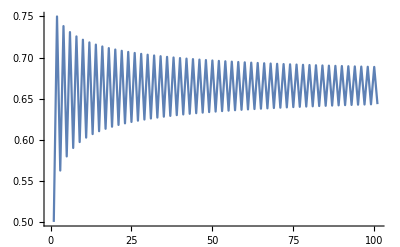

```mathematica
(*динамика системы*)
NestList[k # (1-#)&,0.5,100]//ListLinePlot
```

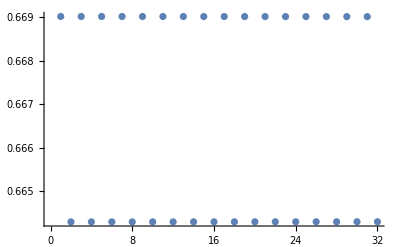

```mathematica
(*предельные точки*)
NestList[k # (1-#)&,0.5,10000]⟦-32;;⟧//ListPlot
```

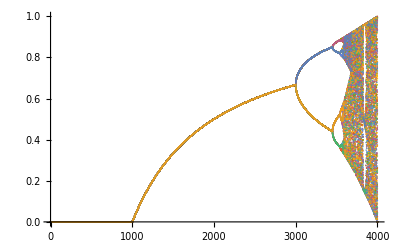

```mathematica
(*полный код для построения бифуркационной диаграммы*)
ListPlot[Table[NestList[k # (1-#)&,0.5,10000]⟦-32;;⟧,{k,0,4,.001}]ᵀ]
```

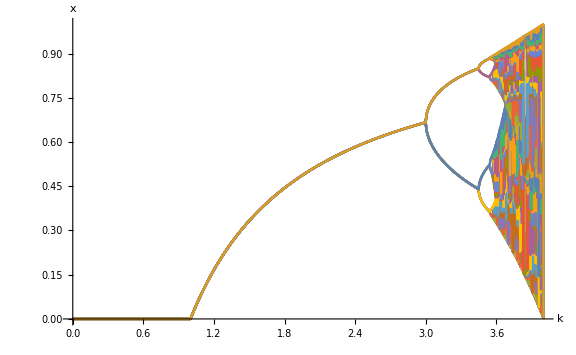

```mathematica
ListLinePlot[Table[Outer[List,{k},Sort[NestList[k #(1-#)&,.5,10000]⟦-32;;⟧]]⟦1⟧,{k,0,4,.001}]ᵀ,AxesLabel->{"k","x"},LabelStyle->Large,ImageSize->Large]
```